```mathematica
total:=Length@Tuples[{1,2,3,4,5,6},6]
listOfDiceOutComes:=Tuples[{1,2,3,4,5,6},6]
total
listOfDiceOutComes
```

46656

{{1,1,1,1,1,1},{1,1,1,1,1,2},{1,1,1,1,1,3},{1,1,1,1,1,4},{1,1,1,1,1,5},{1,1,1,1,1,6},{1,1,1,1,2,1},{1,1,1,1,2,2},{1,1,1,1,2,3},{1,1,1,1,2,4},{1,1,1,1,2,5},{1,1,1,1,2,6},{1,1,1,1,3,1},{1,1,1,1,3,2},{1,1,1,1,3,3},{1,1,1,1,3,4},{1,1,1,1,3,5},{1,1,1,1,3,6},{1,1,1,1,4,1},{1,1,1,1,4,2},{1,1,1,1,4,3},{1,1,1,1,4,4},{1,1,1,1,4,5},{1,1,1,1,4,6},{1,1,1,1,5,1},46606,{6,6,6,6,2,6},{6,6,6,6,3,1},{6,6,6,6,3,2},{6,6,6,6,3,3},{6,6,6,6,3,4},{6,6,6,6,3,5},{6,6,6,6,3,6},{6,6,6,6,4,1},{6,6,6,6,4,2},{6,6,6,6,4,3},{6,6,6,6,4,4},{6,6,6,6,4,5},{6,6,6,6,4,6},{6,6,6,6,5,1},{6,6,6,6,5,2},{6,6,6,6,5,3},{6,6,6,6,5,4},{6,6,6,6,5,5},{6,6,6,6,5,6},{6,6,6,6,6,1},{6,6,6,6,6,2},{6,6,6,6,6,3},{6,6,6,6,6,4},{6,6,6,6,6,5},{6,6,6,6,6,6}}
 |  |  |  |

```mathematica
show:=ContainsAny[{d,f,e},{a,b,c}]
If[show,Print["true"], Print["false"]];
If[True,{Print["true"],Print["foo"]}, Print["false"]]
```

false

true

foo

{Null,Null}

```mathematica
For[i=1,i<10+1,i++,
{
Print[i],
Print["bar"]
}
]
True==True
```

1

bar

2

bar

3

bar

4

bar

5

bar

6

bar

7

bar

8

bar

9

bar

10

bar

True

```mathematica
setOfTrues:={};
sentinel := {};
trueCounts :={};
falseCounts:={};
path={0};
lengthOfListOfDiceOutComes:=Length@listOfDiceOutComes
For[i=1,i<lengthOfListOfDiceOutComes+1,i++,
{
(*TODO - test ContainsAny[listOfDiceOutComes,{4,5,6}] but check for which returns false.*)
(*sizeOfOutCome:=6
For[j=1,sizeOfOutCome+7,j<sizeOfOutCome,
If[ContainsAny[sentinel,{1,2,3}],Print["true"], Print["false"]]
]*)
If[ContainsAll[listOfDiceOutComes[[i]],{1,2,3}]==True,
(*Print["true"],*) 
(*Print["false"]*)
{
(*Print["hi"],*)
AppendTo[setOfTrues,True],
AppendTo[trueCounts,i],
AppendTo[path,path[[i]]+1]
},
{
AppendTo[setOfTrues,False],
AppendTo[falseCounts,i],
AppendTo[path,path[[i]]-1]
}
]
}
]
numberofFalses:=Length[falseCounts]
Length[setOfTrues]
Length[trueCounts]
numberOfTrues:=Length[trueCounts]
numberOfOneTwoThreesBruteForce:=Length[trueCounts]
(*they are the same set;  setOfTrues is admittedly TERRIBLY, MISLEADINGLY Named*)
setOfBooleansOfDoesContainOneTwoThree:=setOfTrues
```

46656

11340

```mathematica
numberOfTrues
numberofFalses
numberOfOneTwoThreesBruteForce
setOfBooleansOfDoesContainOneTwoThree
path
```

11340

35316

11340

{False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,True,True,True,True,True,False,False,True,False,False,False,False,False,46532,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

{0,-1,-2,-3,-4,-5,-6,-7,-8,-7,-8,-9,-10,-11,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20,-21,-22,-23,-24,-25,-26,-27,-28,-29,-30,-31,-32,-33,-34,-33,-34,-35,-36,-37,-38,-37,-38,-39,-40,-39,-38,-37,-36,-35,-34,-35,-36,-35,-36,-37,-38,-39,-40,-39,-40,-41,-42,46523,-23910,-23911,-23912,-23913,-23914,-23915,-23916,-23917,-23918,-23919,-23920,-23921,-23922,-23923,-23924,-23925,-23926,-23927,-23928,-23929,-23930,-23931,-23932,-23933,-23934,-23935,-23936,-23937,-23938,-23939,-23940,-23941,-23942,-23943,-23944,-23945,-23946,-23947,-23948,-23949,-23950,-23951,-23952,-23953,-23954,-23955,-23956,-23957,-23958,-23959,-23960,-23961,-23962,-23963,-23964,-23965,-23966,-23967,-23968,-23969,-23970,-23971,-23972,-23973,-23974,-23975,-23976}
 |  |  |  |

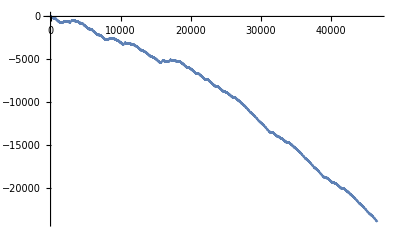

{False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,True,True,True,True,True,False,False,True,False,False,False,False,False,46532,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

```mathematica
ListLinePlot[path]
```

```mathematica
N@numberOfTrues/total
numberOfTrues/total
```

0.243056

```mathematica
35/144
```

35/144

```mathematica
numOf123:=Length@Permutations[{1,2,3,4,5,6},{6}]
numOf123
(* this isn't quite right; there can be 1,2,3,4,4,6
*)
```

720

```mathematica
N@numOf123/total
```

0.0154321

```mathematica
Binomial[6+2-1,3]*Length@Permutations[{1,2,3}]
(*
	No! This mutated version of the BinCoef gives the number of ways to choose 3 objects from a list with replacement; BUT, the order is disregarded, so if 4,4,5 us counted, then 4,5,4 is not.
*)
```

```mathematica
Power[6,3]*Length@Permutations[{1,2,3}]
(*
	Consider 1,2,3, _, _ ,_

    We have to count permutations of that 1,2,3 AND the possible choices for _,_,_.

BUT, this is with 1,2,3 locked in on the left; there may be more or less...

We can count the number of ways to spread 1,2,3 across the 6 slots, but we might end up with repeats.

Currently have no reason to believe that repeats are possible...

as long as we are careful about permuting 1,2,3, AGAIN, we should be ok. 

Meaning, we should probably forego the locked-in 1,2,3 permutation, and just count the number of ways to spread 1,2,3 around the 6 entries.


*)
```

1296

```mathematica
px:=N@1296/total
```

```mathematica
1-px
```

0.972222

```mathematica
Power[1-px,3]
```

0.91896

```mathematica
Factorial[7]/Factorial[4]
```

```mathematica
(*
See:
https://math.stackexchange.com/questions/1423139/arranging-3-items-in-7-spots
*)
```

210

```mathematica
numof123a:=27*Factorial[6]/Factorial[3]
(*
Consider again the 6-string: 1,2,3,_,_,_

The left-hand term gives the number of ways to arrange 6 items in 3 different slots, with order mattering.

So, if we constrain the string with the first three choices as 1,2,3, there'd be 6^3 different instances of the string,
because it'd be counting {1,2,3,_,_,_}, where you generate 6^3 instances by choosing 3 spots for 6 different items (with replacement, order matters).

It remains to find the number of different ways to apply the constraint to the 6-string, i.e.,
how many different ways can three numbers [ 1,2,3] be arranged in 6 slots?

The right-hand term of the product gives us that.
*)
```

```mathematica
numof123a/total
numof123a
total
```

5/72

3240

46656

```mathematica
(*
Prove: You get 6^3 different sets of {1,2,3,_,_,_), by generating instances from choosing 3 numbers from a set of 6, with replacement, and order mattering.

The set of 6 numbers is {1,2,3,4,5,6}'

Length@Tuples[{1,2,3,4,5,6},6]


*)

Tuples[{4,5,6},3]
```

{{4,4,4},{4,4,5},{4,4,6},{4,5,4},{4,5,5},{4,5,6},{4,6,4},{4,6,5},{4,6,6},{5,4,4},{5,4,5},{5,4,6},{5,5,4},{5,5,5},{5,5,6},{5,6,4},{5,6,5},{5,6,6},{6,4,4},{6,4,5},{6,4,6},{6,5,4},{6,5,5},{6,5,6},{6,6,4},{6,6,5},{6,6,6}}